## Init

```mathematica
Needs["StringCode`"];
InitStringCode[<|"theory" -> "TypeII","CFT"->"FlatSpace", "conventions"-> "TypeII-Ashoke", "bracket"->"Flat"|>];
```

```mathematica
vis3Boxes=StringCode`OPE`TypeII`FlatSpace`TensorStructuresVisualize`visualizeTensorStructures[<|"vector"->{},"spinor"->{{a1,"chiral"},{a2,"chiral"},{a3,"chiral"}}|>,<|"vector"->{},"spinor"->{{a4,"antichiral"}}|>,"MaxGroups"->60,(*show first 60 structures*)"ImageSize"->400,"BoxWidth"->1.6,"BoxHeight"->0.9,"LegLength"->0.6];
```

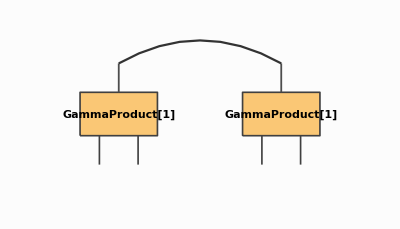
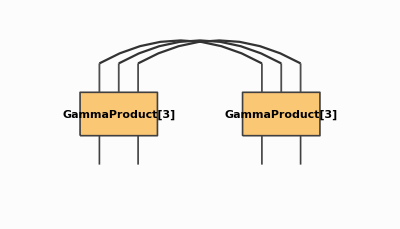
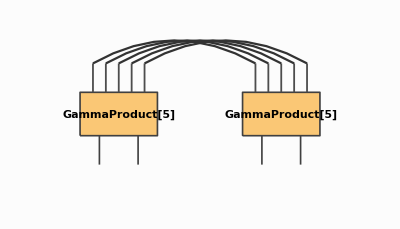
Structure 1 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1)},a1,a4) GammaProduct({CUD,GammaDU(ν1)},a2,a3)
Structure 2 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3)},a1,a4) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3)},a2,a3)
Structure 3 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4),GammaUD(ν5)},a1,a4) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3),GammaUD(ν4),GammaDU(ν5)},a2,a3)

```mathematica
vis3Boxes
```

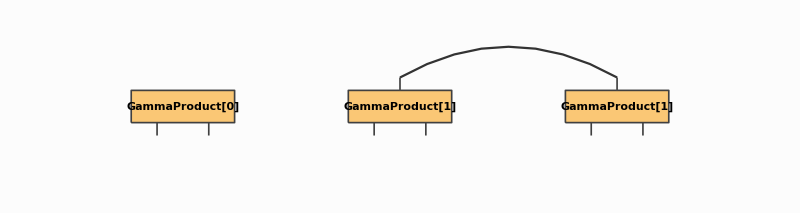
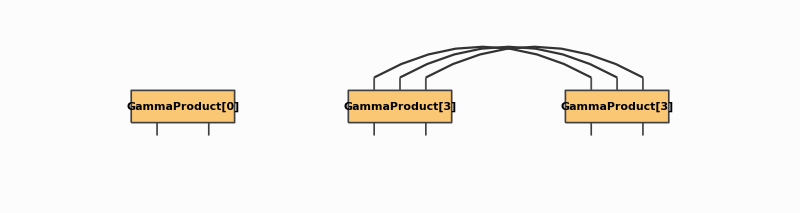
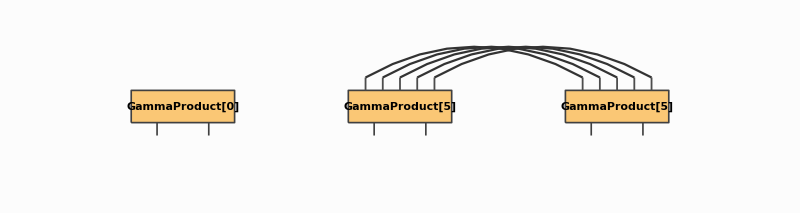
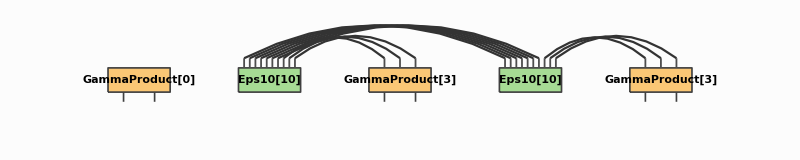
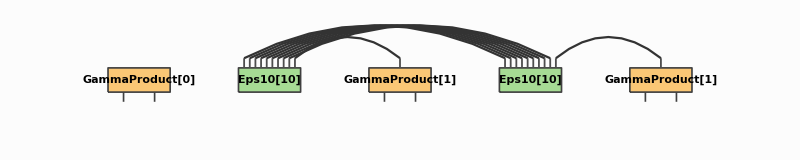
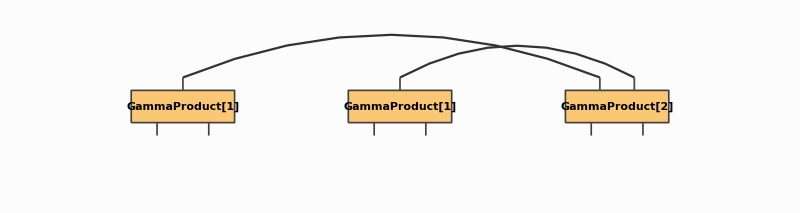
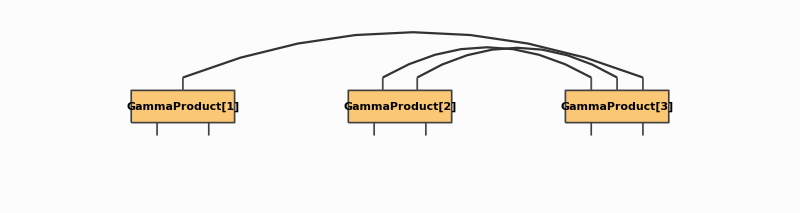
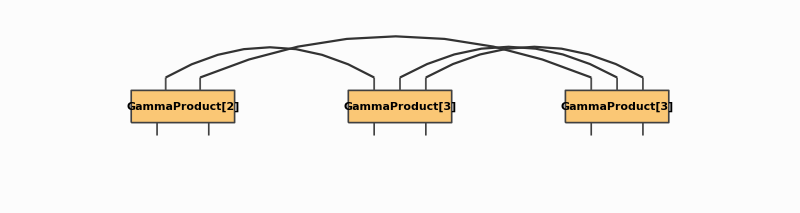
Structure 1 (index permutations: 1)
-Graphics-
GammaProduct({},a6,a1) GammaProduct({CUD,GammaDU(ν1)},a2,a3) GammaProduct({CUD,GammaDU(ν1)},a4,a5)
Structure 2 (index permutations: 1)
-Graphics-
GammaProduct({},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3)},a2,a3) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3)},a4,a5)
Structure 3 (index permutations: 1)
-Graphics-
GammaProduct({},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3),GammaUD(ν4),GammaDU(ν5)},a2,a3) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3),GammaUD(ν4),GammaDU(ν5)},a4,a5)
Structure 4 (index permutations: 1)
-Graphics-
GammaProduct({},a6,a1) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a2,a3) GammaProduct({CUD,GammaDU(ρ4),GammaUD(ρ5),GammaDU(ρ6),Gamma11UU()},a4,a5) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7},{ρ1,ρ2,ρ3}) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7},{ρ4,ρ5,ρ6})
Structure 5 (index permutations: 1)
-Graphics-
GammaProduct({},a6,a1) GammaProduct({CUD,GammaDU(ρ1),Gamma11UU()},a2,a3) GammaProduct({CUD,GammaDU(ρ2),Gamma11UU()},a4,a5) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7,ν8,ν9},{ρ1}) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7,ν8,ν9},{ρ2})
Structure 6 (index permutations: 1)
-Graphics-
GammaProduct({CUD,GammaDU(ν1)},a2,a3) GammaProduct({CUD,GammaDU(ν2)},a4,a5) GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1)
Structure 7 (index permutations: 1)
-Graphics-
GammaProduct({CUD,GammaDU(ν3)},a2,a3) GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3)},a4,a5)
Structure 8 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν3),GammaDU(ν4)},a2,a3) GammaProduct({CUD,GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a4,a5)
Structure 9 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ν3),GammaUD(ν4),GammaDU(ν5)},a2,a3) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3),GammaUD(ν4),GammaDU(ν5)},a4,a5)
Structure 10 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν3),GammaDU(ν4),GammaUD(ν5),GammaDU(ν6)},a2,a3) GammaProduct({CUD,GammaDU(ν2),GammaUD(ν3),GammaDU(ν4),GammaUD(ν5),GammaDU(ν6)},a4,a5)
Structure 11 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a4,a5) GammaProduct({CUD,GammaDU(ν3),GammaUD(ν4),GammaDU(ν5),GammaUD(ν6),GammaDU(ν7)},a2,a3) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7},{ρ1,ρ2,ρ3})
Structure 12 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a2,a3) GammaProduct({CUD,GammaDU(ρ4),GammaUD(ρ5),GammaDU(ρ6),Gamma11UU()},a4,a5) Eps10({ν1,ν3,ν4,ν5,ν6,ν7,ν8},{ρ1,ρ2,ρ3}) Eps10({ν2,ν3,ν4,ν5,ν6,ν7,ν8},{ρ4,ρ5,ρ6})
Structure 13 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ρ4),Gamma11UU()},a4,a5) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a2,a3) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7,ν8,ν9},{ρ4}) Eps10({ν3,ν4,ν5,ν6,ν7,ν8,ν9},{ρ1,ρ2,ρ3})
Structure 14 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2)},a6,a1) GammaProduct({CUD,GammaDU(ρ1),Gamma11UU()},a2,a3) GammaProduct({CUD,GammaDU(ρ2),Gamma11UU()},a4,a5) Eps10({ν1,ν3,ν4,ν5,ν6,ν7,ν8,ν9,ν10},{ρ1}) Eps10({ν2,ν3,ν4,ν5,ν6,ν7,ν8,ν9,ν10},{ρ2})
Structure 15 (index permutations: 1)
-Graphics-
GammaProduct({CUD,GammaDU(ν1)},a2,a3) GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a4,a5)
Structure 16 (index permutations: 1)
-Graphics-
GammaProduct({CUD,GammaDU(ν5)},a2,a3) GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν3),GammaUD(ν4),GammaDU(ν5)},a4,a5)
Structure 17 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν5)},a2,a3) GammaProduct({CUD,GammaDU(ν3),GammaUD(ν4),GammaDU(ν5)},a4,a5)
Structure 18 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν5),GammaDU(ν6)},a2,a3) GammaProduct({CUD,GammaDU(ν2),GammaUD(ν3),GammaDU(ν4),GammaUD(ν5),GammaDU(ν6)},a4,a5)
Structure 19 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ν5),GammaUD(ν6),GammaDU(ν7)},a2,a3) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a4,a5) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7},{ρ1,ρ2,ρ3})
Structure 20 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν2),GammaDU(ν5),GammaUD(ν6),GammaDU(ν7)},a2,a3) GammaProduct({CUD,GammaDU(ν3),GammaUD(ν4),GammaDU(ν5),GammaUD(ν6),GammaDU(ν7)},a4,a5)
Structure 21 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a4,a5) GammaProduct({CUD,GammaDU(ν1),GammaUD(ν5),GammaDU(ν6),GammaUD(ν7),GammaDU(ν8)},a2,a3) Eps10({ν2,ν3,ν4,ν5,ν6,ν7,ν8},{ρ1,ρ2,ρ3})
Structure 22 (index permutations: 1)
-Graphics-
GammaProduct({CUD,GammaDU(ρ1),Gamma11UU()},a4,a5) GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ν5),GammaUD(ν6),GammaDU(ν7),GammaUD(ν8),GammaDU(ν9)},a2,a3) Eps10({ν1,ν2,ν3,ν4,ν5,ν6,ν7,ν8,ν9},{ρ1})
Structure 23 (index permutations: 1)
-Graphics-
GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a2,a3) GammaProduct({CUD,GammaDU(ρ4),GammaUD(ρ5),GammaDU(ρ6),Gamma11UU()},a4,a5) Eps10({ν1,ν2,ν5,ν6,ν7,ν8,ν9},{ρ1,ρ2,ρ3}) Eps10({ν3,ν4,ν5,ν6,ν7,ν8,ν9},{ρ4,ρ5,ρ6})
Structure 24 (index permutations: 1)
-Graphics-
GammaProduct({CUD,GammaDU(ρ4),Gamma11UU()},a4,a5) GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) GammaProduct({CUD,GammaDU(ρ1),GammaUD(ρ2),GammaDU(ρ3),Gamma11UU()},a2,a3) Eps10({ν1,ν5,ν6,ν7,ν8,ν9,ν10},{ρ1,ρ2,ρ3}) Eps10({ν2,ν3,ν4,ν5,ν6,ν7,ν8,ν9,ν10},{ρ4})
Structure 25 (index permutations: 1)
-Graphics-
GammaProduct({CUD,GammaDU(ρ1),Gamma11UU()},a2,a3) GammaProduct({CUD,GammaDU(ρ2),Gamma11UU()},a4,a5) GammaProduct({GammaUD(ν1),GammaDU(ν2),GammaUD(ν3),GammaDU(ν4)},a6,a1) Eps10({ν1,ν2,ν5,ν6,ν7,ν8,ν9,ν10,ν11},{ρ1}) Eps10({ν3,ν4,ν5,ν6,ν7,ν8,ν9,ν10,ν11},{ρ2})

```mathematica
vis3Boxes=StringCode`OPE`TypeII`FlatSpace`TensorStructuresVisualize`visualizeTensorStructures[<|"vector"->{},"spinor"->{{a1,"chiral"},{a2,"chiral"},{a3,"chiral"},{a4,"chiral"},{a5,"chiral"}}|>,<|"vector"->{},"spinor"->{{a6,"chiral"}}|>,"MaxGroups"->60,(*show first 60 structures*)"ImageSize"->800,"BoxWidth"->1.6,"BoxHeight"->0.5,"LegLength"->0.2];

vis3Boxes
```

```mathematica
Quit[]
```

```mathematica
(Timing[BracketProjected[  SF[R[c[0,0], ct[0,0],  expϕf[-1,0],ψ[μ1,0,0], expϕtf[-1,0], ψt[ν1,0,0],expX[k1,0,0]]], SF[R[c[0,0], ct[0,0],  expϕf[-1,0],ψ[μ2,0,0], expϕtf[-1,0], ψt[ν2,0,0],expX[k2,0,0]]],0,0]]/.{Private`z[2,1][{}]->-z0, Private`z[2,2][{}]->z0,Private`zbar[2,1][{}]->-z0bar, Private`zbar[2,2][{}]->z0bar, dot[x___]->0})//Expand//ContractDelta//Simplify
```

{0.089391,{{{-1/8 ⅈ √αp (2 k1[μ2] R[c[0,0],c[1,0],expXHolo[k1,0],expXHolo[k2,0],expϕf[-1,0],ψ[μ1,0,0]]+2 k2[μ2] R[c[0,0],c[1,0],expXHolo[k1,0],expXHolo[k2,0],expϕf[-1,0],ψ[μ1,0,0]]-2 k1[μ1] R[c[0,0],c[1,0],expXHolo[k1,0],expXHolo[k2,0],expϕf[-1,0],ψ[μ2,0,0]]-2 k2[μ1] R[c[0,0],c[1,0],expXHolo[k1,0],expXHolo[k2,0],expϕf[-1,0],ψ[μ2,0,0]]-k1[μ$2220] R[c[0,0],c[1,0],expXHolo[k1,0],expXHolo[k2,0],expϕf[-1,0],ψ[μ$2220,0,0]] δ[μ1,μ2]+k2[μ$2221] R[c[0,0],c[1,0],expXHolo[k1,0],expXHolo[k2,0],expϕf[-1,0],ψ[μ$2221,0,0]] δ[μ1,μ2]),1/8 ⅈ √αp (2 k1[ν2] R[ct[0,0],ct[1,0],expXAntiHolo[k1,0],expXAntiHolo[k2,0],expϕtf[-1,0],ψt[ν1,0,0]]+2 k2[ν2] R[ct[0,0],ct[1,0],expXAntiHolo[k1,0],expXAntiHolo[k2,0],expϕtf[-1,0],ψt[ν1,0,0]]-2 k1[ν1] R[ct[0,0],ct[1,0],expXAntiHolo[k1,0],expXAntiHolo[k2,0],expϕtf[-1,0],ψt[ν2,0,0]]-2 k2[ν1] R[ct[0,0],ct[1,0],expXAntiHolo[k1,0],expXAntiHolo[k2,0],expϕtf[-1,0],ψt[ν2,0,0]]-k1[μ$2235] R[ct[0,0],ct[1,0],expXAntiHolo[k1,0],expXAntiHolo[k2,0],expϕtf[-1,0],ψt[μ$2235,0,0]] δ[ν1,ν2]+k2[μ$2236] R[ct[0,0],ct[1,0],expXAntiHolo[k1,0],expXAntiHolo[k2,0],expϕtf[-1,0],ψt[μ$2236,0,0]] δ[ν1,ν2])}}}}

```mathematica
Timing[Private`generateBasisHolo[0, {-1,-1},{1,1},{-1,0}]]
```

{0.008664,{R[c[0,0],expϕf[-1,0],ψ[normalizedIndex1,0,0]]}}

```mathematica
Timing[Private`generateBasisHolo[0, {-2,-2},{1,1},{-4,0}]]
```

{0.097813,{R[c[0,0],expϕb[-2,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]],R[c[0,0],dX[normalizedIndex1,0,0],expϕb[-2,0]],R[c[0,0],dϕ[0,0],expϕb[-2,0]],R[c[0,0],c[1,0],expϕf[-3,0],ξ[1,0],ψ[normalizedIndex1,1,0]],R[c[0,0],c[1,0],expϕf[-3,0],ξ[1,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0],ψ[normalizedIndex3,0,0]],R[c[0,0],c[1,0],expϕf[-3,0],ξ[2,0],ψ[normalizedIndex1,0,0]],R[c[0,0],c[1,0],expϕf[-3,0],ξ[1,0],ψ[normalizedIndex1,0,0]],R[c[0,0],c[1,0],dX[normalizedIndex1,0,0],expϕf[-3,0],ξ[1,0],ψ[normalizedIndex1,0,0]],R[c[0,0],c[1,0],dϕ[0,0],expϕf[-3,0],ξ[1,0],ψ[normalizedIndex1,0,0]],-R[c[0,0],c[2,0],expϕf[-3,0],ξ[1,0],ψ[normalizedIndex1,0,0]],-R[c[0,0],c[1,0],c[2,0],expϕb[-4,0],ξ[1,0],ξ[2,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]],-R[c[0,0],c[1,0],c[2,0],expϕb[-4,0],ξ[1,0],ξ[3,0]],-R[c[0,0],c[1,0],c[3,0],expϕb[-4,0],ξ[1,0],ξ[2,0]],-R[c[0,0],c[1,0],c[2,0],expϕb[-4,0],ξ[1,0],ξ[2,0]],-R[c[0,0],c[1,0],c[2,0],dX[normalizedIndex1,0,0],expϕb[-4,0],ξ[1,0],ξ[2,0]],-R[c[0,0],c[1,0],c[2,0],dϕ[0,0],expϕb[-4,0],ξ[1,0],ξ[2,0]]}}

```mathematica
Timing[Private`gradeBasisUpToWeightHolo[Private`generateNegativeModesHoloUpToWeight[2]]]
```

{0.002974,<|0→<||>,1/2→<|{0,0}→{{ψ[normalizedIndex1,0,0]}}|>,1→<|{0,0}→{{ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]},{},{dX[normalizedIndex1,0,0]},{dϕ[0,0]}},{0,1}→{{c[2,0]}},{1,-1}→{{ξ[1,0]}},{-1,1}→{{η[0,0]}}|>,3/2→<|{0,0}→{{ψ[normalizedIndex1,1,0]},{ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0],ψ[normalizedIndex3,0,0]},{ψ[normalizedIndex1,0,0]},{dX[normalizedIndex1,0,0],ψ[normalizedIndex1,0,0]},{dϕ[0,0],ψ[normalizedIndex1,0,0]}},{0,1}→{{c[2,0],ψ[normalizedIndex1,0,0]}},{1,-1}→{{ξ[1,0],ψ[normalizedIndex1,0,0]}},{-1,1}→{{η[0,0],ψ[normalizedIndex1,0,0]}}|>,2→<|{0,0}→{{ψ[normalizedIndex1,1,0],ψ[normalizedIndex2,0,0]},{ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0],ψ[normalizedIndex3,0,0],ψ[normalizedIndex4,0,0]},{ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]},{dX[normalizedIndex1,0,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]},{dϕ[0,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]},{dX[normalizedIndex1,1,0]},{dX[normalizedIndex1,0,0],dX[normalizedIndex2,0,0]},{dϕ[1,0]},{dϕ[0,0],dϕ[0,0]},{dX[normalizedIndex1,0,0]},{dϕ[0,0]},{dX[normalizedIndex1,0,0],dϕ[0,0]},{ξ[1,0],η[0,0]}},{0,1}→{{c[2,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]},{c[3,0]},{c[2,0]},{c[2,0],dX[normalizedIndex1,0,0]},{c[2,0],dϕ[0,0]}},{1,-1}→{{ξ[1,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]},{ξ[2,0]},{ξ[1,0]},{dX[normalizedIndex1,0,0],ξ[1,0]},{dϕ[0,0],ξ[1,0]}},{-1,1}→{{η[0,0],ψ[normalizedIndex1,0,0],ψ[normalizedIndex2,0,0]},{η[1,0]},{η[0,0]},{dX[normalizedIndex1,0,0],η[0,0]},{dϕ[0,0],η[0,0]}},{0,-1}→{{b[0,0]}},{1,0}→{{c[2,0],ξ[1,0]}},{-1,2}→{{c[2,0],η[0,0]}}|>|>}

```mathematica
Timing[R[expX[k1,0,0],expX[k,0,0],dX[μ,0,0],dX[ν,0,0],expϕf[-1,0],dX[ρ,0,0],dX[λ,0,0],c[0,0],b[0,0],c[1,0],expϕf[-1,0],b[1,0]]]
```

{0.003396,R[b[0,0],b[1,0],c[0,0],c[1,0],dX[λ,0,0],dX[μ,0,0],dX[ν,0,0],dX[ρ,0,0],expX[k,0,0],expX[k1,0,0],expϕb[-2,0]]}

```mathematica
Timing[Private`symbolListToR[{ expX[k1,0,0],expX[k,0,0],dX[μ,0,0],dX[ν,0,0],expϕf[-1,0],dX[ρ,0,0],dX[λ,0,0],c[0,0],b[0,0],c[1,0],expϕf[-1,0],b[1,0]}]]
```

{0.001899,R[b[0,0],b[1,0],c[0,0],c[1,0],dX[λ,0,0],dX[μ,0,0],dX[ν,0,0],dX[ρ,0,0],expX[k,0,0],expX[k1,0,0],expϕb[-2,0]]}

```mathematica
Timing[R @@ Sort[{c[0,0], c[1,0],expXHolo[k1,0],expXHolo[k2,0],dϕ[0,0] }]]
```

{0.000245,R[c[0,0],c[1,0],dϕ[0,0],expXHolo[k1,0],expXHolo[k2,0]]}

```mathematica
Timing[Private`symbolListToR[{c[0,0], c[1,0],expXHolo[k1,0],expXHolo[k2,0],dϕ[0,0] }]]
```

0.000111

0.000221

{0.000702,R[c[0,0],c[1,0],dϕ[0,0],expXHolo[k1,0],expXHolo[k2,0]]}

```mathematica
Timing[R @@ {c[0,0], c[1,0] ,expXHolo[k1,0],expXHolo[k2,0],dϕ[0,0]  }]
```

{0.000412,R[c[0,0],c[1,0],dϕ[0,0],expXHolo[k1,0],expXHolo[k2,0]]}

```mathematica
Quit[]
```

```mathematica
ClearAll[ReplaceDummyIndices];
ReplaceDummyIndices[expr_]:=Module[{dummies,replacements},(*Find all dummy index symbols like μ$1234*)dummies=DeleteDuplicates@Cases[expr,s_Symbol/;StringMatchQ[SymbolName[s],___~~"$"~~NumberString],{0,Infinity}];
(*Replace each dummy with base name plus running number:μ$1234->μ1*)replacements=Thread[dummies->MapIndexed[With[{base=StringReplace[SymbolName[#1],"$"~~__->""]},ToExpression[base<>ToString[#2[[1]]]]]&,dummies]];
expr/. replacements];
```

```mathematica
(Timing[BracketProjected[ lambda1[μ],lambdabar2[ν],0,0]]/.{Private`z1[]->-z0, Private`z2[]->z0,Private`zbar1[]->-z0bar, Private`zbar2[]->z0bar, dot[x___]->0})//Expand//ContractDelta//ReplaceDummyIndices//Simplify
```

{0.429622,{{1/16 (-4 R[c[0,0],expϕf[-1,0],ProfileXHolo[λ1[μ],{},0],ProfileXHolo[λbar2[ν],{},0],ψ[μ,0,0]]+√αp (R[c[0,0],c[1,0],expϕb[-2,0],ProfileXHolo[λ1[μ1],{μ1},0],ProfileXHolo[λbar2[ν],{},0],ξ[1,0]]-R[c[0,0],c[1,0],expϕb[-2,0],ProfileXHolo[λ1[μ2],{},0],ProfileXHolo[λbar2[ν],{μ2},0],ξ[1,0]]+R[c[0,0],c[1,0],expϕb[-2,0],ProfileXHolo[λ1[μ3],{μ3},0],ProfileXHolo[λbar2[ν],{},0],ξ[1,0]]-R[c[0,0],c[1,0],expϕb[-2,0],ProfileXHolo[λ1[μ4],{},0],ProfileXHolo[λbar2[ν],{μ4},0],ξ[1,0]]+4 R[c[0,0],c[1,0],expϕb[-2,0],ProfileXHolo[λ1[μ],{},0],ProfileXHolo[λbar2[ν],{},0],ξ[1,0]] der[λ1[μ]][μ]+4 R[c[0,0],c[1,0],expϕb[-2,0],ProfileXHolo[λ1[μ],{},0],ProfileXHolo[λbar2[ν],{},0],ξ[1,0]] der[λbar2[ν]][μ])),1/8 (-2 R[ct[0,0],expϕtf[-1,0],ProfileXAntiHolo[λ1[μ],{},0],ProfileXAntiHolo[λbar2[ν],{},0],ψt[ν,0,0]]+√αp (R[ct[0,0],ct[1,0],expϕtb[-2,0],ProfileXAntiHolo[λ1[μ],{},0],ProfileXAntiHolo[λbar2[ν],{ν},0],ξt[1,0]]-R[ct[0,0],ct[1,0],expϕtb[-2,0],ProfileXAntiHolo[λ1[μ],{ν},0],ProfileXAntiHolo[λbar2[ν],{},0],ξt[1,0]]+2 R[ct[0,0],ct[1,0],expϕtb[-2,0],ProfileXAntiHolo[λ1[μ],{},0],ProfileXAntiHolo[λbar2[ν],{},0],ξt[1,0]] (der[λ1[μ]][ν]+der[λbar2[ν]][ν]))),-1}}}

```mathematica
(Timing[BracketProjected[ lambda1[μ],lambda2[ν],0,0]]/.{Private`z1[]->-z0, Private`z2[]->z0,Private`zbar1[]->-z0bar, Private`zbar2[]->z0bar, dot[x___]->0})//Expand//ContractDelta//ReplaceDummyIndices//Simplify
```

{3.09938,{{1/16 √αp (R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[ν],{},0],ProfileXHolo[λ2[ν],{μ1},0],ψ[μ1,0,0]]+R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[ν],{},0],ProfileXHolo[λ2[ν],{μ2},0],ψ[μ2,0,0]]-R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[ν],{μ3},0],ProfileXHolo[λ2[ν],{},0],ψ[μ3,0,0]]-R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[ν],{μ4},0],ProfileXHolo[λ2[ν],{},0],ψ[μ4,0,0]]-4 R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[μ],{},0],ProfileXHolo[λ2[ν],{},0],ψ[ν,0,0]] der[λ1[μ]][μ]+4 R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[μ],{},0],ProfileXHolo[λ2[ν],{},0],ψ[μ,0,0]] der[λ1[μ]][ν]-4 R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[μ],{},0],ProfileXHolo[λ2[ν],{},0],ψ[ν,0,0]] der[λ2[ν]][μ]+4 R[c[0,0],c[1,0],expϕf[-1,0],ProfileXHolo[λ1[μ],{},0],ProfileXHolo[λ2[ν],{},0],ψ[μ,0,0]] der[λ2[ν]][ν]),1/4 R[ct[0,0],expϕtb[-2,0],ProfileXAntiHolo[λ1[μ],{},0],ProfileXAntiHolo[λ2[ν],{},0],ξt[1,0]],1}}}

```mathematica
lambda1[μ_]:= SF[c[0],ct[0], ψ[μ,0],ξt[1], expϕf[-1], expϕtb[-2],ProfileX[λ1[μ],{}]]
```

```mathematica
lambda2[μ_]:= SF[c[0],ct[0], ψ[μ,0],ξt[1], expϕf[-1], expϕtb[-2],ProfileX[λ2[μ],{}]]
```

```mathematica
lambdabar1[μ_]:=SF[c[0],ct[0],ξ[1], ψt[μ,0], expϕb[-2], expϕtf[-1], ProfileX[λbar1[μ],{}]]
```

```mathematica
lambdabar2[μ_]:=SF[c[0],ct[0],ξ[1], ψt[μ,0], expϕb[-2], expϕtf[-1], ProfileX[λbar2[μ],{}]]
```

```mathematica
Timing[(Plus @@ Map[ReplaceDummyIndices,(Bracket[lambda1[μ],lambdabar2[ν]]//Expand//ContractDelta)/.{Plus->List}] )]
```

{7.4595,-1/16 √αp R[c[0,0],ct[0,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[λ1[μ],{},0,0],ProfileX[λbar2[ν],{μ},0,0],ξ[1,0],ψt[ν,0,0]]-1/16 √αp R[c[0,0],ct[0,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[λ1[μ],{μ},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ψt[ν,0,0]]+1/32 √αp R[c[0,0],ct[0,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[λ1[μ1],{},0,0],ProfileX[λbar2[ν],{μ1},0,0],ξ[1,0],ψt[ν,0,0]]-1/32 √αp R[c[0,0],ct[0,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[λ1[μ1],{μ1},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ψt[ν,0,0]]-3/32 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[μ],{},0,0],ProfileX[λbar2[ν],{ν},0,0],ξt[1,0],ψ[μ,0,0]]-1/32 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[μ],{ν},0,0],ProfileX[λbar2[ν],{},0,0],ξt[1,0],ψ[μ,0,0]]+5/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{},0,0],ProfileX[λbar2[ν],{μ,ν},0,0],ξ[1,0],ξt[1,0]]+1/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{},0,0],ProfileX[λbar2[ν],{ν,μ},0,0],ξ[1,0],ξt[1,0]]+3/32 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{μ},0,0],ProfileX[λbar2[ν],{ν},0,0],ξ[1,0],ξt[1,0]]+1/32 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{ν},0,0],ProfileX[λbar2[ν],{μ},0,0],ξ[1,0],ξt[1,0]]+3/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{μ,ν},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ξt[1,0]]-1/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{ν,μ},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ξt[1,0]]-1/32 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{},0,0],ProfileX[λbar2[ν],{μ1,ν},0,0],ξ[1,0],ξt[1,0]]-1/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{},0,0],ProfileX[λbar2[ν],{ν,μ1},0,0],ξ[1,0],ξt[1,0]]+3/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{μ1},0,0],ProfileX[λbar2[ν],{ν},0,0],ξ[1,0],ξt[1,0]]-1/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{ν},0,0],ProfileX[λbar2[ν],{μ1},0,0],ξ[1,0],ξt[1,0]]+1/64 αp R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{ν,μ1},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ξt[1,0]]+5/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{},0,0],ProfileX[λbar2[ν],{μ,ν},0,0],ξ[1,0],ξt[1,0]]+1/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{},0,0],ProfileX[λbar2[ν],{ν,μ},0,0],ξ[1,0],ξt[1,0]]+3/32 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{μ},0,0],ProfileX[λbar2[ν],{ν},0,0],ξ[1,0],ξt[1,0]]+1/32 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{ν},0,0],ProfileX[λbar2[ν],{μ},0,0],ξ[1,0],ξt[1,0]]+3/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{μ,ν},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ξt[1,0]]-1/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ],{ν,μ},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ξt[1,0]]-1/32 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{},0,0],ProfileX[λbar2[ν],{μ1,ν},0,0],ξ[1,0],ξt[1,0]]-1/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{},0,0],ProfileX[λbar2[ν],{ν,μ1},0,0],ξ[1,0],ξt[1,0]]+3/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{μ1},0,0],ProfileX[λbar2[ν],{ν},0,0],ξ[1,0],ξt[1,0]]-1/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{ν},0,0],ProfileX[λbar2[ν],{μ1},0,0],ξ[1,0],ξt[1,0]]+1/64 αp R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtb[-2,0],ProfileX[λ1[μ1],{ν,μ1},0,0],ProfileX[λbar2[ν],{},0,0],ξ[1,0],ξt[1,0]]}

```mathematica
Timing[(Plus @@ Map[ReplaceDummyIndices,(Bracket[lambda1[μ],lambda2[ν],1/2]//Expand//ContractDelta)/.{Plus->List}] )]
```

{47.6447,-1/16 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[μ],{},0,0],ProfileX[λ2[ν],{μ},0,0],ξt[1,0],ψ[ν,0,0]]+1/16 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[μ],{},0,0],ProfileX[λ2[ν],{ν},0,0],ξt[1,0],ψ[μ,0,0]]-1/16 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[μ],{μ},0,0],ProfileX[λ2[ν],{},0,0],ξt[1,0],ψ[ν,0,0]]+1/16 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[μ],{ν},0,0],ProfileX[λ2[ν],{},0,0],ξt[1,0],ψ[μ,0,0]]+1/32 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[ν],{},0,0],ProfileX[λ2[ν],{μ1},0,0],ξt[1,0],ψ[μ1,0,0]]-1/32 √αp R[c[0,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[λ1[ν],{μ1},0,0],ProfileX[λ2[ν],{},0,0],ξt[1,0],ψ[μ1,0,0]]}

```mathematica
Timing[Plus @@ Map[ReplaceDummyIndices,(Bracket[SF[c[0], ct[0], expϕf[-1], expϕtf[-1],ψ[μ,0], ψt[ν,0], ProfileX[h1[μ, ν], {}]], SF[c[0], ct[0], expϕf[-1], expϕtf[-1],ψ[ρ,0], ψt[σ,0], ProfileX[h2[ρ,σ],{}]],3]//Expand//ContractDelta)/.{Plus->List}]]
```

```mathematica
(actBRST[SF[c[0], ct[0],  expϕf[-1],ψ[μ,0], expϕtb[-2], ξt[1], ProfileX[V[μ],{}]] + SF[c[0], ct[0],   expϕb[-2], ξ[1], expϕtf[-1],ψt[μ,0], ProfileX[V[μ],{}]]]//ContractDelta)/.{αp->1}
```

1/4 R[c[0,0],ct[0,0],expϕb[-2,0],ProfileX[V[μ],{μ},0,0],ηt[0,0],ξ[1,0]]+1/4 R[c[0,0],ct[0,0],expϕtb[-2,0],ProfileX[V[μ],{μ},0,0],η[0,0],ξt[1,0]]-1/2 R[c[0,0],ct[0,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[V[μ],{μ$19112},0,0],ψ[μ$19112,0,0],ψt[μ,0,0]]-1/2 R[c[0,0],ct[0,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[V[μ],{μ$19423},0,0],ψ[μ,0,0],ψt[μ$19423,0,0]]-1/4 R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[V[μ],{μ$19111,μ$19111},0,0],ξ[1,0],ψt[μ,0,0]]-1/4 R[c[0,0],c[1,0],ct[0,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[V[μ],{μ$19322,μ$19322},0,0],ξt[1,0],ψ[μ,0,0]]+1/4 R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[V[μ],{μ$19223,μ$19223},0,0],ξ[1,0],ψt[μ,0,0]]+1/4 R[c[0,0],ct[0,0],ct[1,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[V[μ],{μ$19422,μ$19422},0,0],ξt[1,0],ψ[μ,0,0]]

```mathematica
metric = 4 SF[c[0], ct[0],  expϕf[-1],ψ[μ,0], expϕtf[-1], ψt[ν,0], ProfileX[h[μ, ν],{}]];
```

```mathematica
ghostD = SF[c[0], ct[0],  η[0], expϕtb[-2],ξt[1], ProfileX[ϕ,{}]]-SF[c[0], ct[0],  expϕb[-2],ξ[1], ηt[0], ProfileX[ϕ,{}]];
```

```mathematica
auxField = 1/2(SF[c[1],c[0],ct[0], expϕf[-1], ψ[μ,0], expϕtb[-2] ,ξt[1], ProfileX[A[μ],{}]] + SF[c[1],c[0], ct[0], expϕb[-2], ξ[1], expϕtf[-1], ψt[μ,0], ProfileX[A[μ],{}]] + SF[ct[1],c[0],ct[0], expϕf[-1], ψ[μ,0], expϕtb[-2] ,ξt[1], ProfileX[A[μ],{}]] + SF[ct[1],c[0], ct[0], expϕb[-2], ξ[1], expϕtf[-1], ψt[μ,0], ProfileX[A[μ],{}]]);
```

```mathematica
Timing[actBRST[metric]//Expand//ContractDelta]/.{αp->1}
```

{0.256298,-R[c[0,0],ct[0,0],expϕf[-1,0],ProfileX[h[μ,ν],{ν},0,0],ηt[0,0],ψ[μ,0,0]]-R[c[0,0],ct[0,0],expϕtf[-1,0],ProfileX[h[μ,ν],{μ},0,0],η[0,0],ψt[ν,0,0]]-R[c[0,0],c[1,0],ct[0,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[h[μ,ν],{μ$9087,μ$9087},0,0],ψ[μ,0,0],ψt[ν,0,0]]+R[c[0,0],ct[0,0],ct[1,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[h[μ,ν],{μ$9217,μ$9217},0,0],ψ[μ,0,0],ψt[ν,0,0]]}

```mathematica
Timing[actBRST[ghostD]//Expand//ContractDelta]/.{αp->1}
```

{0.445879,1/2 R[c[0,0],ct[0,0],expϕf[-1,0],ProfileX[ϕ,{μ$9885},0,0],ηt[0,0],ψ[μ$9885,0,0]]+1/2 R[c[0,0],ct[0,0],expϕtf[-1,0],ProfileX[ϕ,{μ$10270},0,0],η[0,0],ψt[μ$10270,0,0]]+1/4 R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],ProfileX[ϕ,{μ$9884,μ$9884},0,0],ηt[0,0],ξ[1,0]]+1/4 R[c[0,0],c[1,0],ct[0,0],expϕtb[-2,0],ProfileX[ϕ,{μ$10150,μ$10150},0,0],η[0,0],ξt[1,0]]-1/4 R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],ProfileX[ϕ,{μ$10032,μ$10032},0,0],ηt[0,0],ξ[1,0]]-1/4 R[c[0,0],ct[0,0],ct[1,0],expϕtb[-2,0],ProfileX[ϕ,{μ$10269,μ$10269},0,0],η[0,0],ξt[1,0]]}

```mathematica
Timing[(actBRST[auxField]//Expand//ContractDelta)/.{αp->1}]
```

{1.3046,-1/4 R[c[0,0],ct[0,0],expϕf[-1,0],ProfileX[A[μ],{},0,0],ηt[0,0],ψ[μ,0,0]]-1/4 R[c[0,0],ct[0,0],expϕtf[-1,0],ProfileX[A[μ],{},0,0],η[0,0],ψt[μ,0,0]]+1/8 R[c[0,0],c[1,0],ct[0,0],expϕb[-2,0],ProfileX[A[μ],{μ},0,0],ηt[0,0],ξ[1,0]]+1/8 R[c[0,0],c[1,0],ct[0,0],expϕtb[-2,0],ProfileX[A[μ],{μ},0,0],η[0,0],ξt[1,0]]-1/8 R[c[0,0],ct[0,0],ct[1,0],expϕb[-2,0],ProfileX[A[μ],{μ},0,0],ηt[0,0],ξ[1,0]]-1/8 R[c[0,0],ct[0,0],ct[1,0],expϕtb[-2,0],ProfileX[A[μ],{μ},0,0],η[0,0],ξt[1,0]]-1/4 R[c[0,0],c[1,0],ct[0,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[A[μ],{μ$13355},0,0],ψ[μ$13355,0,0],ψt[μ,0,0]]-1/4 R[c[0,0],c[1,0],ct[0,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[A[μ],{μ$13802},0,0],ψ[μ,0,0],ψt[μ$13802,0,0]]+1/4 R[c[0,0],ct[0,0],ct[1,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[A[μ],{μ$13951},0,0],ψ[μ$13951,0,0],ψt[μ,0,0]]+1/4 R[c[0,0],ct[0,0],ct[1,0],expϕf[-1,0],expϕtf[-1,0],ProfileX[A[μ],{μ$14381},0,0],ψ[μ,0,0],ψt[μ$14381,0,0]]+1/8 R[c[0,0],c[1,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[A[μ],{μ$13518,μ$13518},0,0],ξ[1,0],ψt[μ,0,0]]-1/8 R[c[0,0],c[1,0],ct[0,0],ct[1,0],expϕb[-2,0],expϕtf[-1,0],ProfileX[A[μ],{μ$13950,μ$13950},0,0],ξ[1,0],ψt[μ,0,0]]+1/8 R[c[0,0],c[1,0],ct[0,0],ct[1,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[A[μ],{μ$13801,μ$13801},0,0],ξt[1,0],ψ[μ,0,0]]-1/8 R[c[0,0],c[1,0],ct[0,0],ct[1,0],expϕf[-1,0],expϕtb[-2,0],ProfileX[A[μ],{μ$14251,μ$14251},0,0],ξt[1,0],ψ[μ,0,0]]}

```mathematica
Timing[Bracket[SF[c[0],ct[0],expϕf[-1],ψ[ρ,0],expϕtb[-2],ξt[1]],SF[expX[p],c[0],ct[0],expϕf[-1],ψ[μ,0],dX[μ,0],expϕtf[-1],ψt[ν,0],dXt[ν,0]]]]
```

```mathematica
actBRST[SF[c[1],c[0], ct[0], expϕf[-1],ψ[μ,0], expϕtb[-2], ξt[1]]]
```

```mathematica
Timing[1/2(actBRST[SF[c[1],c[0], ct[0], expϕf[-1],ψ[μ,0], expϕtb[-2], ξt[1]]]+ actBRST[SF[ct[1],c[0], ct[0], expϕf[-1],ψ[μ,0], expϕtb[-2], ξt[1]]] + actBRST[SF[c[1],c[0], ct[0], expϕb[-2], ξ[1], expϕtf[-1],ψt[μ,0]]] + actBRST[SF[ct[1],c[0], ct[0], expϕb[-2], ξ[1], expϕtf[-1],ψt[μ,0]]])//Expand//ContractDelta]
```

{0.648846,-1/4 R[c[0,0],ct[0,0],expϕf[-1,0],ηt[0,0],ψ[μ,0,0]]-1/4 R[c[0,0],ct[0,0],expϕtf[-1,0],η[0,0],ψt[μ,0,0]]}

# Testing

```mathematica
Gmatter[z]
```

ⅈ √2 R[dX[μ$5129,0,z],ψ[μ$5129,0,z]]

```mathematica
(*** testing β γ OPE ***)
Taylor[(OPE[βghost[z],γghost[w]]//Expand)/.w->0,0,0,1]//Expand
Taylor[(OPE[γghost[z],βghost[w]]//Expand)/.w->0,0,0,1]//Expand
```

-1/z+R[dϕ[0,0]]-z R[η[0,0],ξ[1,0]]-z^2 R[η[0,0],ξ[2,0]]+z^2 R[dϕ[0,0],η[0,0],ξ[1,0]]+z^3 R[dϕ[0,0],η[0,0],ξ[2,0]]

1/z+R[dϕ[0,0]]+z R[η[0,0],ξ[1,0]]+z^2 R[η[1,0],ξ[1,0]]+z^2 R[dϕ[0,0],η[0,0],ξ[1,0]]+z^3 R[dϕ[0,0],η[1,0],ξ[1,0]]

```mathematica
(*** checking BRST transformation of b and β ghosts ***)
Polar[Taylor[OPE[jBRST[z],R[b[0,w]]]/.w->0//Expand,0,0,2],z,0]-1/z Ttotal[0]//Expand//replaceUniqueSymbols
Polar[Taylor[OPE[jBRST[z],R[βghost[w]]]/.w->0//Expand,0,0,2],z,0]- 1/z (-1/2  Gtotal[0])//Expand//replaceUniqueSymbols
```

-(3 R[dϕ[0,0]])/(2 z^2)-R[b[0,0],c[0,0]]/z^2

0

```mathematica
(*** checking PCO ***)
Polar[Taylor[(OPE[jBRST[z],R[ξ[0,w]]]//Expand)/.w->0,0,0,2],z,0]-1/z PCO[0]//Expand//replaceUniqueSymbols
```

R[b[0,0],expϕb[2,0],η[0,0]]/(4 z^2)

```mathematica
(*** checking BRST current is weight 1 primary ***)
pol1=Polar[Taylor[(OPE[Ttotal[z],jBRST[w]]//Expand//Contract)/.w->0,0,0,2],z,0];
pol2=Polar[Taylor[jBRST[z]/z^2,0,0,2],z,0];
(pol1- pol2//replaceUniqueSymbols)/.{δ[μ,μ]->1}//Expand
```

0

```mathematica
(*** checking nilpotency of BRST charge ***)
poltest=Polar[Taylor[(OPE[jBRST[z],jBRST[w]]//Expand//Contract)/.w->0,0,0,3],z,0]
```

-(5 R[c[0,0],c[1,0]])/(2 z^3)+1/(4 z^2)(-5 R[c[0,0],c[2,0]]-2 ⅈ √2 R[c[0,0],dX[μ$5156,0,0],expϕf[1,0],η[0,0],ψ[μ$5156,0,0]]+2 ⅈ √2 R[c[0,0],dX[μ$5158,0,0],expϕf[1,0],η[0,0],ψ[μ$5158,0,0]]-2 R[c[0,0],c[1,0],ψ[μ$5155,0,0],ψ[μ$5157,0,0]] δ[μ$5155,μ$5157]+2 ⅈ √2 R[c[0,0],dX[μ$5155,0,0],expϕf[1,0],η[0,0],ψ[μ$5158,0,0]] δ[μ$5155,μ$5158]+ⅈ √2 R[c[0,0],dX[μ$5158,0,0],expϕf[1,0],η[0,0],ψ[μ$5155,0,0]] δ[μ$5155,μ$5158]-ⅈ √2 R[c[0,0],dX[μ$5156,0,0],expϕf[1,0],η[0,0],ψ[μ$5157,0,0]] δ[μ$5156,μ$5157]-2 ⅈ √2 R[c[0,0],dX[μ$5157,0,0],expϕf[1,0],η[0,0],ψ[μ$5156,0,0]] δ[μ$5156,μ$5157]+R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5156,0,0],ψ[μ$5158,0,0]] δ[μ$5156,μ$5158])+1/(8 z)(-R[expϕb[2,0],η[0,0],η[3,0]]-R[expϕb[2,0],η[1,0],η[2,0]]-8 R[c[0,0],c[1,0],dX[μ$5155,0,0],dX[μ$5155,0,0]]-8 R[c[0,0],c[1,0],dX[μ$5157,0,0],dX[μ$5157,0,0]]-4 R[c[0,0],c[1,0],ψ[μ$5155,0,0],ψ[μ$5155,1,0]]-4 R[c[0,0],c[1,0],ψ[μ$5157,0,0],ψ[μ$5157,1,0]]-5 R[dϕ[0,0],expϕb[2,0],η[0,0],η[2,0]]-3 R[dϕ[1,0],expϕb[2,0],η[0,0],η[1,0]]-2 R[b[0,0],c[0,0],expϕb[2,0],η[0,0],η[2,0]]-2 R[b[0,0],c[1,0],expϕb[2,0],η[0,0],η[1,0]]-2 R[b[1,0],c[0,0],expϕb[2,0],η[0,0],η[1,0]]-4 ⅈ √2 R[c[0,0],dX[μ$5156,0,0],expϕf[1,0],η[0,0],ψ[μ$5156,1,0]]-4 ⅈ √2 R[c[0,0],dX[μ$5156,1,0],expϕf[1,0],η[0,0],ψ[μ$5156,0,0]]+4 ⅈ √2 R[c[0,0],dX[μ$5158,0,0],expϕf[1,0],η[1,0],ψ[μ$5158,0,0]]-6 ⅈ √2 R[c[1,0],dX[μ$5156,0,0],expϕf[1,0],η[0,0],ψ[μ$5156,0,0]]-2 ⅈ √2 R[c[1,0],dX[μ$5158,0,0],expϕf[1,0],η[0,0],ψ[μ$5158,0,0]]+2 R[dX[μ$5155,0,0],dX[μ$5155,0,0],expϕb[2,0],η[0,0],η[1,0]]+2 R[dX[μ$5157,0,0],dX[μ$5157,0,0],expϕb[2,0],η[0,0],η[1,0]]-6 R[dϕ[0,0],dϕ[0,0],expϕb[2,0],η[0,0],η[1,0]]+R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5155,0,0],ψ[μ$5155,1,0]]+R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5157,0,0],ψ[μ$5157,1,0]]-4 R[b[0,0],c[0,0],dϕ[0,0],expϕb[2,0],η[0,0],η[1,0]]+4 ⅈ √2 R[c[0,0],dX[μ$5158,0,0],dϕ[0,0],expϕf[1,0],η[0,0],ψ[μ$5158,0,0]]+16 R[c[0,0],c[1,0],dX[μ$5155,0,0],dX[μ$5157,0,0]] δ[μ$5155,μ$5157]+2 R[c[0,0],c[1,0],ψ[μ$5155,0,0],ψ[μ$5157,1,0]] δ[μ$5155,μ$5157]-6 R[c[0,0],c[1,0],ψ[μ$5155,1,0],ψ[μ$5157,0,0]] δ[μ$5155,μ$5157]-2 R[c[0,0],c[2,0],ψ[μ$5155,0,0],ψ[μ$5157,0,0]] δ[μ$5155,μ$5157]+4 ⅈ √2 R[c[0,0],dX[μ$5155,1,0],expϕf[1,0],η[0,0],ψ[μ$5158,0,0]] δ[μ$5155,μ$5158]+4 ⅈ √2 R[c[0,0],dX[μ$5158,0,0],expϕf[1,0],η[0,0],ψ[μ$5155,1,0]] δ[μ$5155,μ$5158]+4 ⅈ √2 R[c[1,0],dX[μ$5155,0,0],expϕf[1,0],η[0,0],ψ[μ$5158,0,0]] δ[μ$5155,μ$5158]+2 ⅈ √2 R[c[1,0],dX[μ$5158,0,0],expϕf[1,0],η[0,0],ψ[μ$5155,0,0]] δ[μ$5155,μ$5158]+2 ⅈ √2 R[c[0,0],dX[μ$5156,0,0],expϕf[1,0],η[0,0],ψ[μ$5157,1,0]] δ[μ$5156,μ$5157]-2 ⅈ √2 R[c[0,0],dX[μ$5156,0,0],expϕf[1,0],η[1,0],ψ[μ$5157,0,0]] δ[μ$5156,μ$5157]-2 ⅈ √2 R[c[0,0],dX[μ$5156,1,0],expϕf[1,0],η[0,0],ψ[μ$5157,0,0]] δ[μ$5156,μ$5157]-4 ⅈ √2 R[c[0,0],dX[μ$5157,0,0],expϕf[1,0],η[0,0],ψ[μ$5156,1,0]] δ[μ$5156,μ$5157]-4 ⅈ √2 R[c[0,0],dX[μ$5157,0,0],expϕf[1,0],η[1,0],ψ[μ$5156,0,0]] δ[μ$5156,μ$5157]-2 ⅈ √2 R[c[0,0],dX[μ$5156,0,0],dϕ[0,0],expϕf[1,0],η[0,0],ψ[μ$5157,0,0]] δ[μ$5156,μ$5157]-4 ⅈ √2 R[c[0,0],dX[μ$5157,0,0],dϕ[0,0],expϕf[1,0],η[0,0],ψ[μ$5156,0,0]] δ[μ$5156,μ$5157]-4 R[dX[μ$5156,0,0],dX[μ$5158,0,0],expϕb[2,0],η[0,0],η[1,0]] δ[μ$5156,μ$5158]+2 R[expϕb[2,0],η[0,0],η[1,0],ψ[μ$5156,1,0],ψ[μ$5158,0,0]] δ[μ$5156,μ$5158]+R[expϕb[2,0],η[0,0],η[2,0],ψ[μ$5156,0,0],ψ[μ$5158,0,0]] δ[μ$5156,μ$5158]+2 R[dϕ[0,0],expϕb[2,0],η[0,0],η[1,0],ψ[μ$5156,0,0],ψ[μ$5158,0,0]] δ[μ$5156,μ$5158])

```mathematica
poltotalderiv=Polar[Taylor[-1/(8 z^2)2 ⅈ √2 R[c[0,z],dX[μ,0,z],expϕf[1,z],η[0,z],ψ[μ,0,z]]-R[b[0,z],c[0,z],expϕb[2,z],η[0,z],η[1,z]]/(4 z^2)+(-R[expϕb[2,z],η[0,z],η[2,z]])/(8 z^2)+(-3 R[dϕ[0,z],expϕb[2,z],η[0,z],η[1,z]])/(8 z^2),0,0,2],z,0];
((poltest-  poltotalderiv//replaceUniqueSymbols)/.{δ[μ,μ]->1})+O[z]
```

-(5 R[c[0,0],c[1,0]])/(2 z^3)+1/(8 z^2)(-10 R[c[0,0],c[2,0]]+R[expϕb[2,0],η[0,0],η[2,0]]+3 R[dϕ[0,0],expϕb[2,0],η[0,0],η[1,0]]+2 R[b[0,0],c[0,0],expϕb[2,0],η[0,0],η[1,0]]+2 ⅈ √2 R[c[0,0],dX[μ,0,0],expϕf[1,0],η[0,0],ψ[μ,0,0]])+O[z]^1

```mathematica
(*** checking T T OPE ***)
(Polar[Taylor[((OPE[Ttotal[z],Ttotal[w]]//Simplify//Contract)/.w->0)-(1/z^2 Ttotal[0]+1/z^2 Ttotal[z]),0,0,2],z,0]//replaceUniqueSymbols)/.{δ[μ,μ]->1}//Expand
```

0

```mathematica
tripgrav=OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar],RaisedGraviton[μ3,ν3,k3,z3,z3bar]];
```

```mathematica
Graviton[μ_,ν_,k_,z_,zbar_]:=R[c[0,z],ct[0,zbar],expϕf[-1,z],ψ[μ,0,z],expϕtf[-1,zbar],ψt[ν,0,zbar],expX[k,z,zbar]]

PictureRaiseL[vert_,z1_,z1bar_]:=Block[{w,x},SeriesCoefficient[(Taylor[OPE[PCO[w],vert]//ContractDelta,z1,z1bar,0]/.w->z1+x)+O[x],0]]
PictureRaiseR[vert_,z1_,z1bar_]:=Block[{w,x},SeriesCoefficient[(Taylor[OPE[PCObar[w],vert]//ContractDelta,z1,z1bar,0]/.w->z1bar+x)+O[x],0]]
PictureRaiseLR[vert_,z1_,z1bar_]:=PictureRaiseR[PictureRaiseL[vert,z1,z1bar],z1,z1bar]
```

```mathematica
RaisedGraviton[μ1_,ν1_,k1_,z1_,z1bar_]:=PictureRaiseLR[Graviton[μ1,ν1,k1,z1,z1bar],z1,z1bar]//Expand

tripgrav=OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar],RaisedGraviton[μ3,ν3,k3,z3,z3bar]];

(*** graviton 3-point amplitude ***)tripgravamp=Vev[tripgrav/.{z1->x,z1bar->x,z2->1,z2bar->1,z3->0,z3bar->0}/.{dot[k1,k2]->0,dot[k1,k3]->0,dot[k2,k3]->0}]//Simplify//Expand//ContractDelta//Simplify

(e1[μ1] e1[ν1] e2[μ2] e2[ν2] e3[μ3] e3[ν3] tripgravamp//Expand//ContractDelta)//.{(f1_[μ_] f2_[μ_]):>dot[f1,f2]}/.{dot[e3,k2]->-dot[e3,k1]}//Simplify
```

-1/(32 (-1+x)^2)R[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expϕb[-2,0],expϕtb[-2,0]] (k1[μ3] δ[μ1,μ2]+x k2[μ3] δ[μ1,μ2]-(-1+x) (k3[μ2] δ[μ1,μ3]-k3[μ1] δ[μ2,μ3])) (k1[ν3] δ[ν1,ν2]+x k2[ν3] δ[ν1,ν2]-(-1+x) (k3[ν2] δ[ν1,ν3]-k3[ν1] δ[ν2,ν3]))

-1/32 (-dot[e1,k3] dot[e2,e3]+dot[e1,e3] dot[e2,k3]+dot[e1,e2] dot[e3,k1])^2 R[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expϕb[-2,0],expϕtb[-2,0]]

```mathematica
SimpleRaisedGraviton[μ_,ν_,k_,z_,zbar_]:=(RaisedGraviton[μ,ν,k,z,zbar]/.{η[a__]:>0,ηt[a__]:>0})
IntegratedSimpleRaisedGraviton[μ_,ν_,k_,z_,zbar_]:=Block[{w},(w-z) (w-zbar) OPE[R[bt[0,w],b[0,w]],SimpleRaisedGraviton[μ,ν,k,z,zbar]]/.{b[a__]:>0,bt[a__]:>0}//Simplify//Expand]
FourGravCorr=Corr[OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar]],
OPE[SimpleRaisedGraviton[μ3,ν3,k3,z3,z3bar],IntegratedSimpleRaisedGraviton[μ4,ν4,k4,z4,z4bar]]];
```

```mathematica
FourGravCorr
```

```mathematica
VevFourGravCorr=Vev[FourGravCorr/.{z3->1/x,z3bar->1/x,z1->1,z1bar->1,z2->0,z2bar->0}/.{dot[k1,k4]->dot[k2,k3],dot[k2,k4]->dot[k1,k3],dot[k3,k4]->dot[k1,k2]}]//Simplify
```

1/(256 (-1+x z4)^3 (-1+x z4bar)^3)(1/x^2)^(1/2 dot[k2,k3]) ((-1+x)^2/x^2)^(1/2 dot[k1,k3]) ((-1+z4) (-1+z4bar))^(1/2 (-2+dot[k2,k3])) (z4 z4bar)^(1/2 (-2+dot[k1,k3])) (((-1+x z4) (-1+x z4bar))/x^2)^(1/2 (2+dot[k1,k2])) CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]] (-k2[μ3] k2[μ4] δ[μ1,μ2]+x k2[μ3] k2[μ4] δ[μ1,μ2]+z4 k2[μ3] k2[μ4] δ[μ1,μ2]+x z4 k2[μ3] k2[μ4] δ[μ1,μ2]-2 x^2 z4 k2[μ3] k2[μ4] δ[μ1,μ2]-2 x z4^2 k2[μ3] k2[μ4] δ[μ1,μ2]+x^2 z4^2 k2[μ3] k2[μ4] δ[μ1,μ2]+x^3 z4^2 k2[μ3] k2[μ4] δ[μ1,μ2]+x^2 z4^3 k2[μ3] k2[μ4] δ[μ1,μ2]-x^3 z4^3 k2[μ3] k2[μ4] δ[μ1,μ2]+x z4 k2[μ3] k3[μ4] δ[μ1,μ2]-x^2 z4 k2[μ3] k3[μ4] δ[μ1,μ2]-x z4^2 k2[μ3] k3[μ4] δ[μ1,μ2]+x^3 z4^2 k2[μ3] k3[μ4] δ[μ1,μ2]+x^2 z4^3 k2[μ3] k3[μ4] δ[μ1,μ2]-x^3 z4^3 k2[μ3] k3[μ4] δ[μ1,μ2]-k2[μ4] k4[μ3] δ[μ1,μ2]+x k2[μ4] k4[μ3] δ[μ1,μ2]+z4 k2[μ4] k4[μ3] δ[μ1,μ2]-x^2 z4 k2[μ4] k4[μ3] δ[μ1,μ2]-x z4^2 k2[μ4] k4[μ3] δ[μ1,μ2]+x^2 z4^2 k2[μ4] k4[μ3] δ[μ1,μ2]+x z4 k3[μ4] k4[μ3] δ[μ1,μ2]-x^2 z4 k3[μ4] k4[μ3] δ[μ1,μ2]-x z4^2 k3[μ4] k4[μ3] δ[μ1,μ2]+x^2 z4^2 k3[μ4] k4[μ3] δ[μ1,μ2]+x k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x z4 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-2 x^2 z4 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+2 x^2 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+x^3 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x^3 z4^3 k2[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x^2 z4 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+x^2 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]+x^3 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-x^3 z4^3 k3[μ4] k3[μ$5628] δ[μ1,μ$5628] δ[μ2,μ3]-k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+2 x z4 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-2 x^2 z4 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x^2 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x^3 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]+x z4 k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x^2 z4 k4[μ3] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x z4 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+2 x^2 z4 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-2 x^2 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-x^3 z4^2 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x^3 z4^3 k2[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x^2 z4 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-x^2 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-x^3 z4^2 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]+x^3 z4^3 k3[μ4] k3[μ$5628] δ[μ1,μ3] δ[μ2,μ$5628]-z4 (-1+x z4) k1[μ4] ((-1+x) (-1+x z4) k2[μ3] δ[μ1,μ2]-(-1+x) k4[μ3] δ[μ1,μ2]+x (-1+x z4) k3[μ$5628] (δ[μ1,μ$5628] δ[μ2,μ3]-δ[μ1,μ3] δ[μ2,μ$5628]))+k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-2 x z4 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+2 x^2 z4 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+x^2 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x^3 z4^2 k2[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]-x z4 k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+x^2 z4 k4[μ3] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+(-1+x z4) k1[μ3] (z4 (-1+x z4) k1[μ4] δ[μ1,μ2]+(-1+z4) (-1+x z4) k2[μ4] δ[μ1,μ2]-x z4 k3[μ4] δ[μ1,μ2]+x z4^2 k3[μ4] δ[μ1,μ2]+k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-x z4 k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ4]-k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630]+x z4 k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5630])-2 x z4 δ[μ1,μ2] δ[μ3,μ4]+2 x^2 z4 δ[μ1,μ2] δ[μ3,μ4]+2 x z4^2 δ[μ1,μ2] δ[μ3,μ4]-2 x^2 z4^2 δ[μ1,μ2] δ[μ3,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]-x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ$5628] δ[μ3,μ4]-x k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ$5630] δ[μ3,μ4]+x k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5628] δ[μ2,μ4] δ[μ3,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]+x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ$5628] δ[μ3,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]+x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ$5630] δ[μ2,μ3] δ[μ$5628,μ4]+x k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ$5630] δ[μ$5628,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]+x z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ$5630] δ[μ$5628,μ4]-x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]-x^3 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ4] δ[μ2,μ3] δ[μ$5628,μ$5630]-x k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]+x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]-x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ3] δ[μ2,μ4] δ[μ$5628,μ$5630]+x z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]-x^2 z4 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]-x z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]+x^2 z4^2 k3[μ$5628] k4[μ$5630] δ[μ1,μ2] δ[μ3,μ4] δ[μ$5628,μ$5630]) (k2[ν3] k2[ν4] δ[ν1,ν2]-x k2[ν3] k2[ν4] δ[ν1,ν2]-z4bar k2[ν3] k2[ν4] δ[ν1,ν2]-x z4bar k2[ν3] k2[ν4] δ[ν1,ν2]+2 x^2 z4bar k2[ν3] k2[ν4] δ[ν1,ν2]+2 x z4bar^2 k2[ν3] k2[ν4] δ[ν1,ν2]-x^2 z4bar^2 k2[ν3] k2[ν4] δ[ν1,ν2]-x^3 z4bar^2 k2[ν3] k2[ν4] δ[ν1,ν2]-x^2 z4bar^3 k2[ν3] k2[ν4] δ[ν1,ν2]+x^3 z4bar^3 k2[ν3] k2[ν4] δ[ν1,ν2]-x z4bar k2[ν3] k3[ν4] δ[ν1,ν2]+x^2 z4bar k2[ν3] k3[ν4] δ[ν1,ν2]+x z4bar^2 k2[ν3] k3[ν4] δ[ν1,ν2]-x^3 z4bar^2 k2[ν3] k3[ν4] δ[ν1,ν2]-x^2 z4bar^3 k2[ν3] k3[ν4] δ[ν1,ν2]+x^3 z4bar^3 k2[ν3] k3[ν4] δ[ν1,ν2]+k2[ν4] k4[ν3] δ[ν1,ν2]-x k2[ν4] k4[ν3] δ[ν1,ν2]-z4bar k2[ν4] k4[ν3] δ[ν1,ν2]+x^2 z4bar k2[ν4] k4[ν3] δ[ν1,ν2]+x z4bar^2 k2[ν4] k4[ν3] δ[ν1,ν2]-x^2 z4bar^2 k2[ν4] k4[ν3] δ[ν1,ν2]-x z4bar k3[ν4] k4[ν3] δ[ν1,ν2]+x^2 z4bar k3[ν4] k4[ν3] δ[ν1,ν2]+x z4bar^2 k3[ν4] k4[ν3] δ[ν1,ν2]-x^2 z4bar^2 k3[ν4] k4[ν3] δ[ν1,ν2]+x k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-x z4bar k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-2 x^2 z4bar k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]+2 x^2 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]+x^3 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-x^3 z4bar^3 k2[ν4] k3[μ$5629] δ[ν1,ν3] δ[ν2,μ$5629]-x^2 z4bar k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]+x^2 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]+x^3 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]-x^3 z4bar^3 k3[μ$5629] k3[ν4] δ[ν1,ν3] δ[ν2,μ$5629]-x k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]+x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν3] δ[ν2,μ$5631]-k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+x k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+2 x z4bar k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]-2 x^2 z4bar k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]-x^2 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+x^3 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]-k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]+x k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]+x z4bar k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]-x^2 z4bar k4[μ$5631] k4[ν3] δ[ν1,ν4] δ[ν2,μ$5631]-x k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+x z4bar k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+2 x^2 z4bar k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]-2 x^2 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]-x^3 z4bar^2 k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+x^3 z4bar^3 k2[ν4] k3[μ$5629] δ[ν1,μ$5629] δ[ν2,ν3]+x^2 z4bar k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]-x^2 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]-x^3 z4bar^2 k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]+x^3 z4bar^3 k3[μ$5629] k3[ν4] δ[ν1,μ$5629] δ[ν2,ν3]-x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]-x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,μ$5631] δ[ν2,ν3]+x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]+x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν4] δ[ν2,ν3]+z4bar (-1+x z4bar) k1[ν4] ((-1+x) (-1+x z4bar) k2[ν3] δ[ν1,ν2]-(-1+x) k4[ν3] δ[ν1,ν2]-x (-1+x z4bar) k3[μ$5629] (δ[ν1,ν3] δ[ν2,μ$5629]-δ[ν1,μ$5629] δ[ν2,ν3]))+k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-x k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-2 x z4bar k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]+2 x^2 z4bar k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]+x^2 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-x^3 z4bar^2 k2[ν3] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]+k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]-x k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]-x z4bar k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]+x^2 z4bar k4[μ$5631] k4[ν3] δ[ν1,μ$5631] δ[ν2,ν4]+x k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]-x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν3] δ[ν2,ν4]-(-1+x z4bar) k1[ν3] (z4bar (-1+x z4bar) k1[ν4] δ[ν1,ν2]+(-1+z4bar) (-1+x z4bar) k2[ν4] δ[ν1,ν2]-x z4bar k3[ν4] δ[ν1,ν2]+x z4bar^2 k3[ν4] δ[ν1,ν2]-k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+x z4bar k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5631]+k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4]-x z4bar k4[μ$5631] δ[ν1,μ$5631] δ[ν2,ν4])+x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]-x z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,ν4] δ[ν1,ν2] δ[ν3,μ$5631]-x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]-x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,ν4] δ[ν2,μ$5629] δ[ν3,μ$5631]-x k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]+x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,ν4] δ[ν3,μ$5631]+2 x z4bar δ[ν1,ν2] δ[ν3,ν4]-2 x^2 z4bar δ[ν1,ν2] δ[ν3,ν4]-2 x z4bar^2 δ[ν1,ν2] δ[ν3,ν4]+2 x^2 z4bar^2 δ[ν1,ν2] δ[ν3,ν4]-x z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]+x^2 z4bar k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]+x z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[μ$5629,μ$5631] δ[ν1,ν2] δ[ν3,ν4]+x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]-x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]+x^3 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5631] δ[ν2,μ$5629] δ[ν3,ν4]+x k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4]-x z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4]-x^2 z4bar k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4]+x^2 z4bar^2 k3[μ$5629] k4[μ$5631] δ[ν1,μ$5629] δ[ν2,μ$5631] δ[ν3,ν4])

```mathematica
Prefactor=(-1/x)^dot[k2,k3] ((-1+x)/x)^dot[k1,k3] (1-z4)^(-1+1/2 dot[k2,k3]) (1/x-z4)^(1/2 dot[k1,k2]) (-z4)^(-1+1/2 dot[k1,k3]) (1-z4bar)^(-1+1/2 dot[k2,k3]) (1/x-z4bar)^(1/2 dot[k1,k2]) (-z4bar)^(-1+1/2 dot[k1,k3])/(256 x^2 (-1+x z4)^2 (-1+x z4bar)^2) CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]];
```

```mathematica
TwoFactors=List @@(VevFourGravCorr/Prefactor);
```

```mathematica
PrefactorSimplified=Assuming[x>0,((1/x)^dot[k2,k3] (1/x)^dot[k1,k3] (1-z4)^(-1+1/2 dot[k2,k3]) (1/x)^(1/2 dot[k1,k2]) (z4)^(-1+1/2 dot[k1,k3]) (1-z4bar)^(-1+1/2 dot[k2,k3]) (1/x)^(1/2 dot[k1,k2]) (z4bar)^(-1+1/2 dot[k1,k3]) CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]])/(256 x^2 ) /.{dot[k2,k3]->-dot[k1,k2]-dot[k1,k3]}//Simplify];
```

```mathematica
TwoFactorsSimplified=(((TwoFactors//Expand//ContractDelta)//.{k1[m_] k2[m_]:>dot[k1,k2],k1[m_] k3[m_]:>dot[k1,k3],k1[m_] k4[m_]:>dot[k1,k4],k2[m_] k3[m_]:>dot[k2,k3],k2[m_] k4[m_]:>dot[k2,k4],k3[m_] k4[m_]:>dot[k3,k4]}/.{dot[k1,k4]->dot[k2,k3],dot[k2,k4]->dot[k1,k3],dot[k3,k4]->dot[k1,k2]}/.{dot[k2,k3]->-dot[k1,k2]-dot[k1,k3]})+O[x]^2)/.{k4[m_]:>-k1[m]-k2[m]-k3[m]}/.{k1[μ1]->0,k2[μ2]->0,k3[μ3]->0,k1[ν1]->0,k2[ν2]->0,k3[ν3]->0}//Normal//Simplify;
```

```mathematica
(-x^2) PrefactorSimplified/.{CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]]->-4}
```

1/64 (1-z4)^(1/2 (-2-dot[k1,k2]-dot[k1,k3])) z4^(-1+1/2 dot[k1,k3]) (1-z4bar)^(1/2 (-2-dot[k1,k2]-dot[k1,k3])) z4bar^(-1+1/2 dot[k1,k3])

```mathematica
(-x^2) PrefactorSimplified/.{CR[c[0,0],c[1,0],c[2,0],ct[0,0],ct[1,0],ct[2,0],expX[k1,0,0],expX[k2,0,0],expX[k3,0,0],expX[k4,0,0],expϕb[-2,0],expϕtb[-2,0]]->-4}/.{dot[k1,k2]->-1/2 s,dot[k2,k3]->-1/2 t,dot[k1,k3]->-1/2 u}/.{z4^a_ z4bar^a_ (1-z4)^b_ (1-z4bar)^b_:>2Pi Gamma[a+1] Gamma[b+1] Gamma[-1-a-b]/(Gamma[a+b+2] Gamma[-b] Gamma[-a])}//Simplify
```

(π Gamma[1-s/4] Gamma[-u/4] Gamma[(s+u)/4])/(32 Gamma[s/4] Gamma[1-s/4-u/4] Gamma[1+u/4])

```mathematica
TwoFactorsContracted=({e1[μ1]  e2[μ2] e3[μ3] e4[μ4]TwoFactorsSimplified[[1]]/(-x),  e1[ν1]e2[ν2]e3[ν3] e4[ν4]TwoFactorsSimplified[[2]]/x}//Expand//ContractDelta)//.{(f1_[μ_] f2_[μ_]):>dot[f1,f2]}/.{dot[e4,k3]->-dot[e4,k1]-dot[e4,k2]}//Expand;
```

```mathematica
TwoFactorsContracted[[1]]-f1-f2-f3//Expand
```

-f1-f2-f3-((1/x^2)^(1/2 (-dot[k1,k2]-dot[k1,k3])) e1[μ1] e2[μ2] e3[μ3] e4[μ4])/x

```mathematica
f1=Coefficient[TwoFactorsContracted[[1]],dot[e1,e2] dot[e3,e4]] dot[e1,e2] dot[e3,e4]
f2=Coefficient[TwoFactorsContracted[[1]],dot[e1,e3] dot[e2,e4]]dot[e1,e3] dot[e2,e4]
f3=Coefficient[TwoFactorsContracted[[1]],dot[e1,e4] dot[e2,e3]]dot[e1,e4] dot[e2,e3]
```

0

0

0

```mathematica
TripGravGenPCO=Corr[OPE[PCObar[wbar],PCO[w]],OPE[Graviton[μ1,ν1,k1,z1,z1bar],Graviton[μ2,ν2,k2,z2,z2bar],Graviton[μ3,ν3,k3,z3,z3bar]]];
```

$Aborted

```mathematica
(*** graviton 3-point amplitude with PCOs at generic positions ***)
TripGravAmpPCOCorr=Vev[TripGravGenPCO/.{z1->x,z1bar->x,z2->1,z2bar->1,z3->0,z3bar->0}/.{dot[k1,k2]->0,dot[k1,k3]->0,dot[k2,k3]->0}]//Simplify//Expand//ContractDelta//Simplify

((e1[μ1] e1[ν1] e2[μ2] e2[ν2] e3[μ3] e3[ν3] TripGravAmpPCOCorr//Expand//ContractDelta)//.{(f1_[μ_] f2_[μ_]):>dot[f1,f2]}/.{dot[e3,k2]->-dot[e3,k1],dot[e1,k2]->-dot[e1,k3],dot[e2,k1]->-dot[e2,k3],dot[e3,k3]->0,dot[e1,k1]->0,dot[e2,k2]->0})//Simplify
```

expX[k,0,0]